V of t:

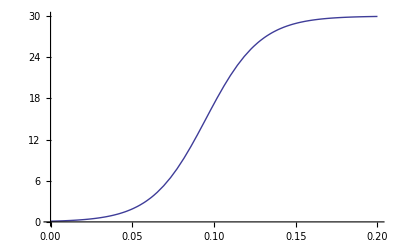

dV/dt (a of t):

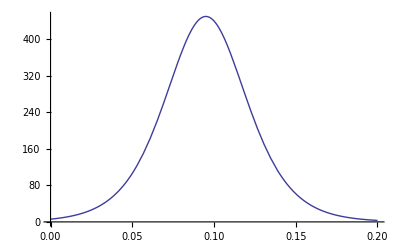

t2 from t1 (remapping event times that were originally based on v=1.0). Therefore, the slope of this plot should approach 1/Vmax as t->inf:

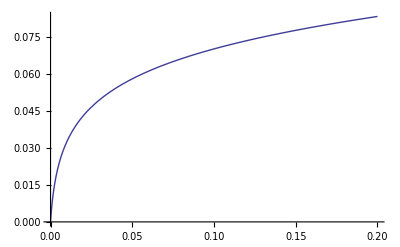

Slope of above plot:

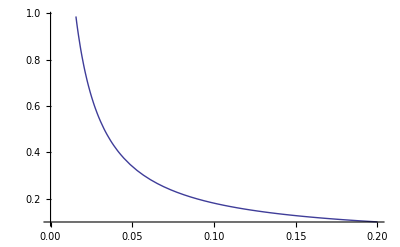

```mathematica
Amax := 450
Vmax := 30
V0 := 0.1
k := 4*Amax/Vmax
c := V0/(Vmax-V0)
tend := 0.2
Print["V of t:"]
Plot[(c*Vmax*E^(k*t))/(1+c*E^(k*t)),{t, 0, tend}]
Print["dV/dt (a of t):"]
Plot[D[(c*Vmax*E^(k*t))/(1+c*E^(k*t)),t] /. t->x, {x, 0, tend}]
t2[t1_]:= 1/k Log[1/c((1+c)E^(k/Vmax*t1)-1)]
Print["t2 from t1 (remapping event times that were originally based on v=1.0). Therefore, the slope of this plot should approach 1/Vmax as t->inf:"]
Plot[t2[x], {x, 0, tend}]
Print["Slope of above plot:"]
Plot[D[t2[t], t] /. t->x, {x, 0, tend}]
```

t2 from t1 (remapping event times that were originally based on v=1.0). This contains both the acceleration and deceleration

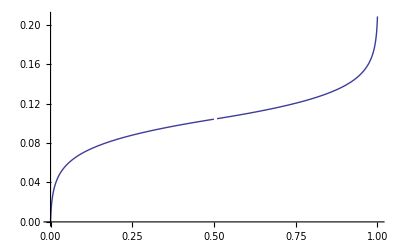

Slope of above plot:

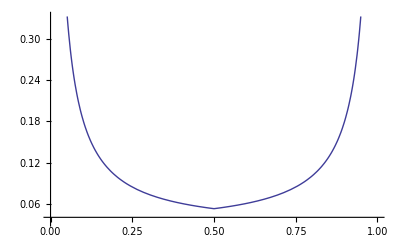

Minimum actual inverse velocity (First item should be greater than the second, indicating that the true velocity is always < the maximum desired

{{0.0526305,{t→0.5}},0.0333333}

```mathematica
(* Conclusion: the above equations are correct *for acceleration*.
Need to add deceleration to this as well, which can just be the mirror of the acceleration portion, and occurs at whatever time 1/2 the distance has been traveled *)
dist := 1
t2acceldecel[t1_] := Piecewise[{{t2[t1], t1<=dist/2},{2*t2[dist/2]-t2[dist-t1], t1 > dist/2}}]
Print["t2 from t1 (remapping event times that were originally based on v=1.0). This contains both the acceleration and deceleration"]
Plot[t2acceldecel[x], {x, 0, dist}]
Print["Slope of above plot:"]
Plot[D[t2acceldecel[t], t] /. t->x, {x, 0, dist}, PlotRange->{{0, dist}, {1/Vmax, 10/Vmax}}]
Print["Minimum actual inverse velocity (First item should be greater than the second, indicating that the true velocity is always < the maximum desired"]
{NMinimize[{D[t2acceldecel[t], t], 0≤ t ≤ dist}, t], N[1/Vmax]}
```